# The Cirac-Zoller Mechanism

Our goal is to construct a 2-qubit CNOT gate which is accomplished by first noting the  identity
-Graphics-
where W is the 2-qubit phase gate given by Eq. 7.49 in the text. To check this relationship we construct the product of gates on the right-hand side of the above equality, and which we recognize as the matrix representation of the CNOT gate shown above. We know how to make Hadamard gates, as described in Section 7.3.1 in the text and Notebook 7.2. The challenge is to construct the two-qubit W gate.

```mathematica
(* we define matrix representations of the following gates *)
ClearAll["Global`*"];
unit={{1,0},{0,1}};
Hadamard=1/Sqrt[2]{{1,1},{1,-1}};
W={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}};
gate=KroneckerProduct[unit,Hadamard].W.KroneckerProduct[unit,Hadamard];
gate // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

Consider the energy diagram for a system comprised of a pair of ion qubits that allow quanta of relative motion (i.e. phonons).
-Graphics-

This diagram illustrates the energy level structure of a system of two qubits and a single phonon quanta. The states are labeled as by Eqs. (7.73) and (7.74) in the text. The Hamiltonian for the system described  by the basis states | i ⟩_3 is  given by Eq. (7.72), or
-Graphics-
and its matrix representation with basis set |0 ⟩_3- |7 ⟩_3, is given by

```mathematica
a={{0,1},{0,0}};
adag={{0,0},{1,0}};
σX={{0,1},{1,0}};
σZ={{1,0},{0,-1}};

H0=-ℏ ω0/2 KroneckerProduct[unit,σZ,unit]-ℏ ω0/2 KroneckerProduct[unit,unit,σZ]+ℏ ν KroneckerProduct[adag.a,unit,unit];
```

The parameters ω_0, ν are defined in section 7.4.2 of the text.

In the Cirac-Zoller scheme, a laser beam of frequency ω = ω_0- ν is impressed on the second ion. This pulse induces transitions between the states |100 ⟩ and |010 ⟩, and between |110⟩ and |011 ⟩. Those transitions are illustrated by the red arrows in the figure above. The interaction Hamiltonian is derived in Section 7.4.2, and for the case where parameter η <1, it is given by the two terms given by Eq. (7.83)

```mathematica
HIa=2 ℏ Δa Cos[ω t+δa]KroneckerProduct[unit,σX,unit];
HIIa=-2 ℏ Δa η Sin[ω t+ δa]KroneckerProduct[a+adag,σX,unit];
```

## Numerical simulation of laser excitation of an ion-phonon system

In the discussion of Section 7.4.3 in the text we invoked the RWA approximation to solve for the time development operator for the system described above. In the simulation given below we perform a full numerical calculation for the time development operator.

First, we define numerical values some of the parameters that characterize the Hamiltonian.

```mathematica
(* initial values *)
ℏ=1;η=0.5;Δa=0.1;ω0= 50.0;δa=0;
ν=ω0/10.0;ω=ω0-ν;
```

```mathematica
(* we construct the Hamiltonian in the interaction picture, as discussed in the text *)
Ham=MatrixExp[I H0 t].( HIa+HIIa).MatrixExp[-I H0 t];
```

```mathematica
(* define the coupled channel wavefunction and the resulting coupled Schrodinger equations *)
psi={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]};
```

```mathematica
eq1=I ℏ c1'[t]==(Ham.psi)[[1]];
eq2=I ℏ c2'[t]==(Ham.psi)[[2]];
eq3=I ℏ c3'[t]==(Ham.psi)[[3]];
eq4=I ℏ c4'[t]==(Ham.psi)[[4]];
eq5=I ℏ c5'[t]==(Ham.psi)[[5]];
eq6=I ℏ c6'[t]==(Ham.psi)[[6]];
eq7=I ℏ c7'[t]==(Ham.psi)[[7]];
eq8=I ℏ c8'[t]==(Ham.psi)[[8]];
```

```mathematica
tRabi=2Pi/Δa/η;

(* we solve these sets of equations for the various boundary conditions for the amplitudes c1[t]..c8[t]*)sols1=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==1.0,c2[0]==0.0,c3[0]==0.0,c4[0]==0.0,c5[0]==0.0,c6[0]==0.0,c7[0]==0.0,c8[0]==0.0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols2=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0.0,c2[0]==1.0,c3[0]==0.0,c4[0]==0.0,c5[0]==0.0,c6[0]==0.0,c7[0]==0.0,c8[0]==0.0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols3=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==1,c4[0]==0,c5[0]==0,c6[0]==0,c7[0]==0,c8[0]==0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols4=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==1,c5[0]==0,c6[0]==0,c7[0]==0,c8[0]==0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols5=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==0,c5[0]==1,c6[0]==0,c7[0]==0,c8[0]==0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols6=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==0,c5[0]==0,c6[0]==1,c7[0]==0,c8[0]==0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols7=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==0,c5[0]==0,c6[0]==0,c7[0]==1,c8[0]==0},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
sols8=Flatten[NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,c1[0]==0,c2[0]==0,c3[0]==0,c4[0]==0,c5[0]==0,c6[0]==0,c7[0]==0,c8[0]==1},{c1,c2,c3,c4,c5,c6,c7,c8},{t,0,tRabi}]];
```

```mathematica
(* cosntruct 8 independent amplitudes from these solutions *)
ψ1[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols1;
ψ2[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols2;
ψ3[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols3;
ψ4[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols4;
ψ5[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols5;
ψ6[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols6;
ψ7[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols7;
ψ8[t_]={c1[t],c2[t],c3[t],c4[t],c5[t],c6[t],c7[t],c8[t]} /. sols8;
```

```mathematica
(* construct the unitary time evolution operator *)
UI[t_]=Transpose[{ψ1[t],ψ2[t],ψ3[t],ψ4[t],ψ5[t],ψ6[t],ψ7[t],ψ8[t]}];
```

```mathematica
(* we plot the interaction picture time development operator between t=0, and t=tRabi *)

g[i_,j_]:=Plot[{Re[UI[t][[i,j]]],Im[UI[t][[i,j]]]},{t,0,tRabi},PlotRange->{-1,1},Frame->True,FrameStyle->Directive[Orange,Dashed],FrameTicks->{False,True},ImageSize->Tiny]
```

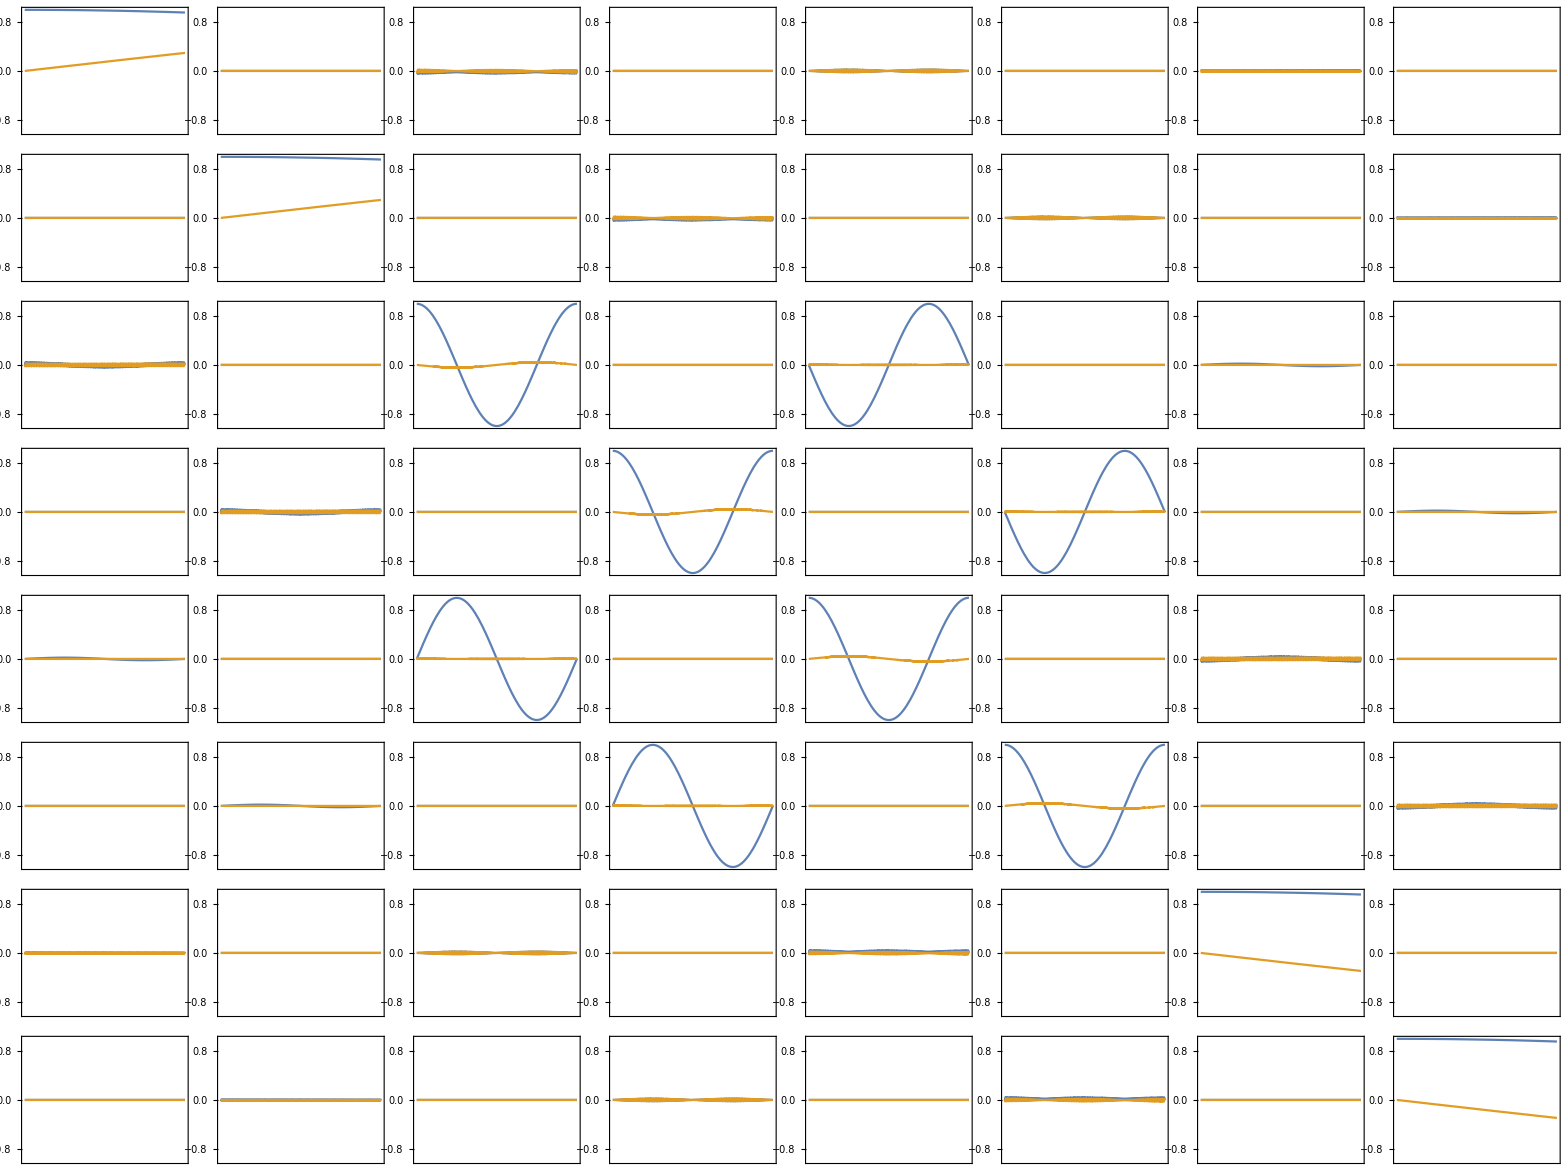
(-Graphics-)

```mathematica
Table[g[i,j],{i,1,8},{j,1,8}] // MatrixForm
```

We now evaluate the time development operator at the end of the pulse time period τ_1 = π /2ηΔ_a. We ignore all contributions whose
 value < 0.08

```mathematica
MatrixForm[Chop[UI[Pi/2/η/Δa],0.08]]
```

(0.996766 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.996766 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.998601 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.998601 | 0 | 0
0 | 0 | 0.998601 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.998601 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.996766 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.996766)

### Construction of the W gate.

Compare this result with that given by Eq. (9.95) in the text, and which was derived within the RWA approximation. Our results are consistent with Eq. (9.95) allowing errors < 8%.  The latter predicts that, within the time period of that pulse,

At the end of this pulse an additional pulse is impressed upon the first ion. That pulse is in resonance, and show by the blue line in the figure above, between state |100⟩ and the highly excited state |8⟩ . The time resulting development operator is given by  Eq. (7.94). For a pulse of period τ_2= π/η Δ_b where we assumed Δ_a= Δ_b, each state is unchanged, except for state |100 ⟩ which undergoes a sign change. Following this pulse we find

Finally, a third pulse is impressed on the second ion. It is equal to that of the first pulse, and using the rules in (2) we obtain the end result

Which realizes the W transformation, and by combining with the Hadamard gate illustrated in Fig. (1), a CNOT gate is realized.